The purpose of this project is to critically examine and evaluate the claims put forth in the paper titled “Grover’s Algorithm Offers No Quantum Advantage”. The paper challenges the widely accepted notion that Grover’s algorithm, a quantum search algorithm, provides a significant speedup compared to classical algorithms. The project aims to investigate the validity of these claims and determine whether Grover’s algorithm truly offers no quantum advantage.

## Introduction

Within the realms of computational complexity theory a search problem is a particular type of computational problem that can be expressed as a binary relation . The essence of this problem lies in the pursuit of identifying a specific structure, denoted as "a," within an object called "b." To solve this problem, an algorithm is considered successful if it can ascertain the existence of at least one such structure and produce one occurrence of it as the output .

Algorithmic complexity refers to the evaluation of the time required for an algorithm to complete when provided with an input of size n . It is crucial for an algorithm to possess scalability, ensuring that it can deliver the result in a reasonable and finite time frame, even for significantly large values of n . To assess scalability, complexity is commonly analyzed asymptotically as n approaches infinity . Although complexity primarily focuses on time considerations, it is occasionally examined in terms of space requirements as well, which pertains to the algorithm' s memory utilization . By analyzing complexity, we gain insights into how algorithms perform and how their efficiency varies with input size .

Search problems play a fundamental role in various domains of computer science, ranging from data retrieval to optimization and decision - making . Optimization problems often involve finding the optimal configuration or arrangement of variables that minimize or maximize a given objective function. Search algorithms can iteratively explore the solution space, evaluating different combinations of variables, until an optimal solution is found. Examples of optimization problems include network routing, resource allocation, scheduling, and parameter tuning in machine learning algorithms. In decision-making contexts, search algorithms are employed to navigate through vast sets of options or alternatives to identify the most suitable choice based on specified criteria. This could involve evaluating different paths in a decision tree, searching for the best move in a game, or selecting the most optimal route in a navigation system.

## Classical Search Algorithm

The classical search algorithm, also known as exhaustive search, is a basic and widely employed method for finding a desired element within a given set . It involves sequentially examining each element of the set until a match is found or the entire set is exhausted . While simple and intuitive, the classical search algorithm can be computationally demanding, especially when dealing with large data sets . As the size of the input increases, the time required for the classical search algorithm to complete also grows linearly, resulting in a time complexity of O(2^n), where n represents the size of the set . This linear growth limits its scalability and efficiency when dealing with significantly large search spaces .

In the context of classical computing, when we have no prior information about the location of a specific target element in an unstructured set of N elements, we are required to examine each element individually in order to find the desired target.

For example, let’s consider a random integer from 1 to 10

```mathematica
ri= RandomInteger[{1,10}]
```

9

And a randomised list of integers from 1 to 10

```mathematica
rs=RandomSample[Table[x,{x,1,10}]]
```

{5,1,6,3,7,10,8,2,9,4}

The classical search algorithm operates by sequentially comparing the target element with each element in the list sequentially, starting from the beginning, until a match is found. Hence, the number of steps is at least equal to the position of the random integer in the list.

```mathematica
Position[rs,ri]
```

{{9}}

```mathematica
If[rs[[#]]==ri,Print[True],Print[False]]&/@Table[i,{i,1,10}];
```

False

False

False

«5 more identical outputs»

True

False

After performing the search process 10 additional times, the position of the random integer within the list is as follows:

```mathematica
NumberSteps=Flatten[Table[Position[RandomSample[Table[x,{x,1,10}]],ri],10]]
```

{8,4,4,6,1,6,2,5,4,3}

Taking the average of the number of steps required

```mathematica
Mean[NumberSteps]//N
```

4.3

Theoretically, when searching for a specific element in a list of N elements, it takes an average of N/2 steps to locate the desired element. By repeating this process 10 more times, we can observe a consistent trend that supports this average.

```mathematica
FindElement[List_,Element_]:=Module[{p},p=Position[List,Element]]
```

{5.95455,5.16667,5.94444,6.04545,6.,5.14286,6.73333,5.55556,6.22222,4.45455}

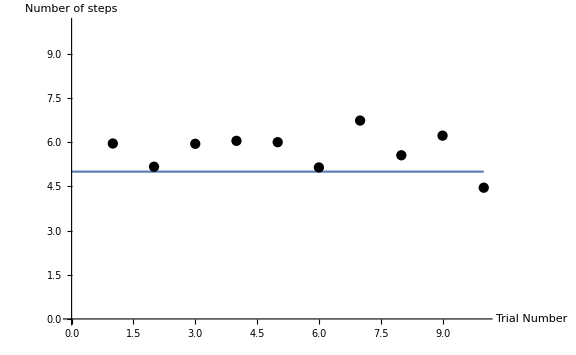

```mathematica
r[x_]:=Table[Clear[r1];FindElement[r1,RandomChoice[r1=RandomInteger[{1,10},x]]],10]
m=Table[N[Mean[Flatten[r[10]]]],10]
Show[Plot[10/2,{xaxis,0,10},PlotLegends->"Theoretical prediction"],ListPlot[m,PlotStyle->Black],PlotRange->{0,10},AxesLabel->{"Trial Number","Number of steps"},ImageSize->Large]
```

In classical computation, it is impossible to solve the search problem in fewer than O(N) evaluations. This is because, on average, one needs to examine approximately half of the elements in the search space.

## Grover’s Algorithm

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Grover' s algorithm, a quantum search algorithm devised by Lov Grover, offers a significant improvement over classical search algorithms for certain types of search problems . By leveraging the principles of quantum computing, Grover' s algorithm achieves a remarkable speedup in the search process . It employs quantum superposition and interference to explore multiple elements of the search space simultaneously, significantly reducing the number of iterations required to find the desired solution . Unlike classical algorithms, Grover' s algorithm exhibits a quadratic speedup, with a time complexity of approximately O(√(2^n)) . This exponential improvement makes Grover' s algorithm highly efficient for large search spaces .

The Grover algorithm is a quantum search algorithm that aims to efficiently find a specific element in an unsorted database. Through a careful design of iterations of a quantum system through an “oracle”, Grover’s algorithm can locate the target element with high probability using significantly fewer evaluations compared to classical approaches.

Consider selecting a bitstring of length “n” that requires a search operation.

```mathematica
n=5;
```

```mathematica
bitstring=StringJoin[ToString/@RandomInteger[{0,1},n]]
```

10101

The optimal number of iterations to find the target element is given by the expression Floor[π/4 √2^n] where 2^n is the total number of elements in the search space. For the sake of clarity, we will consider 2 times of that optimal steps, to show changes in features we compute.

```mathematica
iter=2Floor[π/4 2^(n/2)]
```

8

Create a boolean function such that the chosen bitstring is the only solution.

```mathematica
vlist[bitstring_String]:=Module[{n=StringLength[bitstring],variables},variables=Table[If[StringTake[bitstring,{i,i}]=="0",Not[Symbol["v"<>ToString[i]]],Symbol["v"<>ToString[i]]],{i,n}]]
```

```mathematica
gneralGroverbf=Apply[And,vlist[bitstring]]
```

v1&&!v2&&v3&&!v4&&v5

The oracle in Grover’s algorithm is a vital component that facilitates the identification of the target state within the search space.

Quantum computers effectively boost the probability of identifying the desired item within a search space. This procedure involves amplifying the amplitude of the marked item while simultaneously reducing the amplitudes of the other items. As a result, the final state obtained after measurement will almost certainly correspond to the desired item. The procedure is done using two operators.

We shall consider the phase oracle (and not Boolean oracle).The phase operator changes the phase of the desired state while leaving the other states unchanged. It flips the sign of the amplitude of the marked item, effectively introducing a negative phase factor.

The diffusion operator performs a reflection operation about the average amplitude of the superposition. This reflection amplifies the amplitude of the target state while attenuating the amplitude of the non-target state. It effectively concentrates the amplitude around the target state, making it more distinguishable from the non-target states.

```mathematica
ga=N@QuantumCircuitOperator[{"GroverPhase",gneralGroverbf}];
```

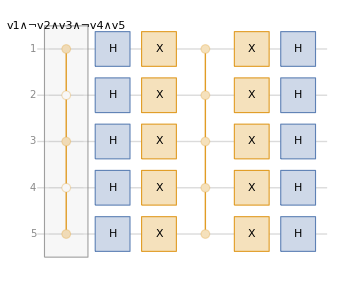

```mathematica
ga["Diagram"]
```

To initiate the procedure, the system begins in a state of uniform superposition. This superposition state provides an initial balance, ensuring that the search process begins without any bias towards a particular state. It also allows the algorithm to simultaneously evaluate multiple states in parallel, exploiting the power of quantum parallelism.

```mathematica
qs=N@QuantumState[{"UniformSuperposition",n}];
```

Iterate the process through the Grover oracle to increase the probability to find the target state.

```mathematica
gaSteps=NestList[ga,qs,2iter+1];
```

Given the state at any step, we can project it into subspace of the solution (yes, it is a bit cheating here, but it does not change the computation; the correct approach is to measure the qubits, and one will get the solution with a given probability).

```mathematica
gaW=QuantumOperator[QuantumState[bitstring]["Dagger"],{{},Range[n]}]
```

QuantumOperator[…]

Now we illustrate it (note after 5 steps, one get the solution with the probability close to one)

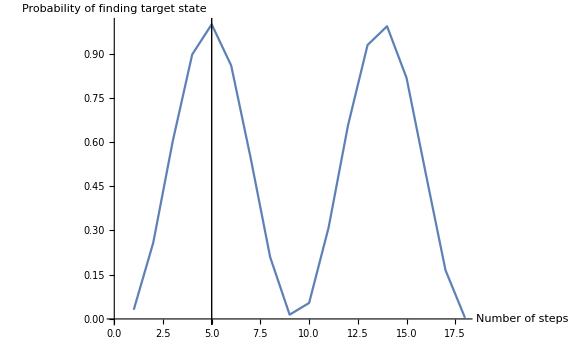

```mathematica
Show[ListLinePlot[gaW[#]["Norm"]^2&/@gaSteps,AxesLabel->{"Number of steps","Probability of finding target state"},ImageSize->Large],Epilog->{InfiniteLine[{5,0},{0,1}]}]
```

Show the numerical values for probability of getting the solution:

```mathematica
gaW[#]["Norm"]^2&/@gaSteps
```

{0.03125,0.258301,0.602425,0.896937,0.999182,0.859637,0.545892,0.209918,0.0144531,0.0541745,0.309843,0.657618,0.929048,0.992657,0.817636,0.488759,0.165328,0.00400334}

Show the max value (as expected, close to one for the solution)

```mathematica
Max[gaW[#]["Norm"]^2&/@gaSteps]
```

0.999182

Number of iterations through the oracle required to maximize the probability of measuring the target element

```mathematica
Flatten[Position[gaW[#]["Norm"]^2&/@gaSteps,Max[gaW[#]["Norm"]^2&/@gaSteps]]]
```

{5}

The authors of the paper I am studying in this computational experiment, mentioned that throughout the process of each iteration, if one treats oracle and diffusion as one single package and apply them on state, the Entanglement Entropy shows an overall Bell-shape increase, with max at the optimal number of steps, but all values less than Log[2]

In order to find Entanglement Entropy, we consider all bipartitioning as follows:

```mathematica
{Range[#],Complement[Range[n],Range[#]]}&/@Range[n]
```

{{{1},{2,3,4,5}},{{1,2},{3,4,5}},{{1,2,3},{4,5}},{{1,2,3,4},{5}},{{1,2,3,4,5},{}}}

Then search over them, and pick the max value of the entropy. For that purpose, we designed the following function. Note this it may take some time to compute, we are monitoring the entropy, as it is computed for each step (that is why we added Echo in the function)

A function to search for different bipartition and get max entropy

```mathematica
entropy[states_,n_]:=Module[{as},Table[{as=With[{s=states[[i]]},AssociationMap[QuantumEntanglementMonotone[N@s,#,"EntanglementEntropy"]&,Range/@Range[n]]],Echo@N@Max[as]},{i,Length[states]}]]
```

Compute the entanglement entropy at each step between the oracle calls for Grover’s Algorithm

```mathematica
ent=entropy[gaSteps,n-1];
```

0. b

0.355917 b

0.576784 b

0.322146 b

0.00685132 b

0.484876 b

0.933924 b

0.863759 b

0.341313 b

0.0222936 b

0.418865 b

0.566504 b

0.251858 b

0.0463121 b

0.578665 b

0.962647 b

0.800639 b

0.248658 b

Plot the entropy, for iteration of oracle and diffusion:

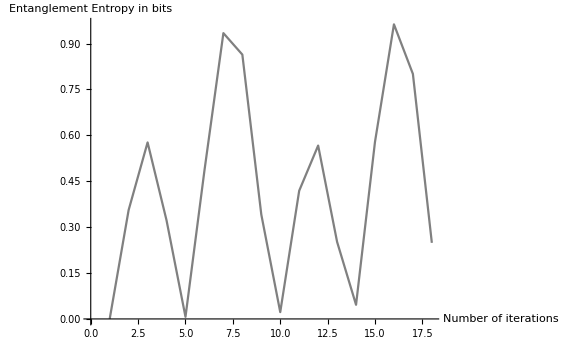

```mathematica
ListLinePlot[ent[[All,-1]],AxesLabel->{"Number of iterations","Entanglement Entropy in bits"},PlotStyle->Gray,PlotLegends->"Grover's oracle (Grey)",ImageSize->Large]
```

## Oracle Described in the Paper: “Grover’s Algorithm Offers No Quantum Advantage”

The logic behind their claim is that when the same “oracle” that defines an implementation of GA on a quantum computer is given to a classical simulator which is limited only by entanglement (a tensor network), can calculate a single oracle circuit with a complexity better than 2^(n/2) they say that their “Quantum Inspired Grover’s Algorithm” solves the GA problem parametrically faster than a quantum computer would.

The authors present their findings by examining various aspects of Grover' s algorithm, such as the time complexity, space complexity, and the impact of noise and imperfections in real - world quantum systems . They argue that the theoretical quadratic speedup offered by Grover' s algorithm may not translate into significant practical advantages due to several factors, including the overhead associated with quantum computations, the limitations of quantum hardware, and the effects of decoherence and noise on quantum states . For that aim, they decompose oracle intro series of simpler controlled-gates, using ancillary qubits.

Construct the oracle described in the paper

```mathematica
oracle[bitstring_String]:=Module[{i,n,firstq,composed,qccn0,oracle2,qccn,diff},
n=StringLength[bitstring];
firstq=If[StringTake[bitstring,1]=="1",QuantumCircuitOperator[{"CNOT"->{1,n+1}}],QuantumCircuitOperator[{"C","NOT"->n+1,{},{1}}]];
composed=RightComposition@@Table[If[StringTake[bitstring,{i+1,i+1}]=="1",QuantumCircuitOperator[{"C","NOT"->i+n+1,{i+n,i+1}}],QuantumCircuitOperator[{"C","NOT"->i+n+1,{i+n},{i+1}}]],{i,n-1}];
qccn0=QuantumCircuitOperator["CNOT"->{2 n,2 n+1}];
oracle2=RightComposition[firstq,composed,qccn0,composed["Dagger"],firstq];
RightComposition[oracle2]]
```

Although not mentioned in the paper, we believe the authors have done the same decomposition, for the diffusion step, too

```mathematica
diffusion[bitstring_String]:=Module[{i,n,firstq,composed,qccn0,qch,oracle2,qcx,qccn,diff},
n=StringLength[bitstring];
firstq=If[StringTake[bitstring,1]=="1",QuantumCircuitOperator[{"CNOT"->{1,n+1}}],QuantumCircuitOperator[{"C","NOT"->n+1,{},{1}}]];
composed=RightComposition@@Table[If[StringTake[bitstring,{i+1,i+1}]=="1",QuantumCircuitOperator[{"C","NOT"->i+n+1,{i+n,i+1}}],QuantumCircuitOperator[{"C","NOT"->i+n+1,{i+n},{i+1}}]],{i,n-1}];
qccn0=QuantumCircuitOperator["CNOT"->{2 n,2 n+1}];
oracle2=RightComposition[firstq,composed,qccn0,composed["Dagger"],firstq];
qch=QuantumCircuitOperator[{"H"}->Range[n]];
RightComposition[qch,oracle2,qch]]
```

Now given the desired bit string, we can construct the overall circuit:

```mathematica
joint=oracle[bitstring]/*diffusion[StringJoin@ConstantArray["0",n]]
```

QuantumCircuitOperator[…]

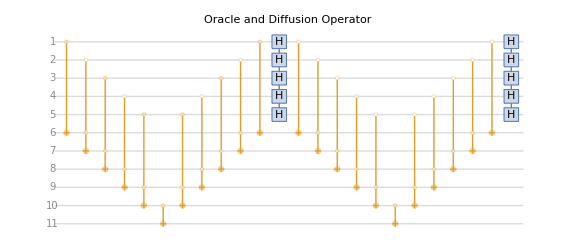

```mathematica
Show[joint["Diagram"],ImageSize->Large,PlotLabel->"Oracle and Diffusion Operator"]
```

```mathematica
oracleoperator=oracle[bitstring];
```

For this oracle , we have to start with 2n+1 qubits with the first n qubits in uniform superposition state and the next n qubits in state “0” and the last qubit in state “-“

```mathematica
initial=QuantumTensorProduct[QuantumState[{"UniformSuperposition",n}],QuantumState[{"Register",n}],QuantumState["-"]]
```

QuantumState[…]

Iterate the process through the oracle to increase the probability to find the target state .

```mathematica
steps3=FoldList[ReverseApplied[Construct],initial,Catenate@Table[joint["Operators"],iter]];
```

Compute max entropy for above steps:

```mathematica
ent3=entropy[steps3,n];
```

0. b

1. b

1.5 b

1.75 b

1.875 b

1.9375 b

1.9375 b

1.875 b

1.875 b

1.70282 b

1.32803 b

0.437004 b

0.437004 b

0.571876 b

0.633915 b

0.688933 b

0.713436 b

0.749606 b

0.749606 b

0.713436 b

0.680806 b

0.614391 b

0.527113 b

0.355917 b

0.355917 b

1.20057 b

1.63727 b

1.89992 b

2.03578 b

2.15397 b

2.15397 b

2.03578 b

2.00191 b

1.83833 b

1.57438 b

0.914023 b

0.914023 b

1.31102 b

1.47711 b

1.60655 b

1.65328 b

1.7473 b

1.7473 b

1.65328 b

1.56089 b

1.37699 b

1.10471 b

0.576784 b

0.576784 b

1.07391 b

1.33014 b

1.50483 b

1.5924 b

1.68233 b

1.68233 b

1.5924 b

1.5463 b

1.4218 b

1.26439 b

0.890586 b

0.890586 b

1.57255 b

1.84498 b

2.00966 b

2.04071 b

2.15831 b

2.15831 b

2.04071 b

1.90262 b

1.63641 b

1.18862 b

0.322146 b

0.322146 b

0.470088 b

0.545412 b

0.60334 b

0.631761 b

0.663415 b

0.663415 b

0.631761 b

0.60987 b

0.561215 b

0.506656 b

0.389008 b

0.389008 b

1.29421 b

1.67896 b

1.85318 b

1.85385 b

1.90625 b

1.90625 b

1.85385 b

1.74008 b

1.49868 b

1.00548 b

0.00685132 b

0.00685132 b

0.00856943 b

0.00942396 b

0.0102099 b

0.0105923 b

0.0110315 b

0.0110315 b

0.0105923 b

0.0102017 b

0.0094018 b

0.00851069 b

0.00672813 b

0.00672813 b

1.00527 b

1.50866 b

1.76533 b

1.89724 b

1.96889 b

1.96889 b

1.89724 b

1.89668 b

1.72603 b

1.36097 b

0.484876 b

0.484876 b

0.637743 b

0.707487 b

0.768951 b

0.796028 b

0.836848 b

0.836848 b

0.796028 b

0.759019 b

0.683799 b

0.583925 b

0.388268 b

0.388268 b

1.20983 b

1.6347 b

1.89314 b

2.02644 b

2.14469 b

2.14469 b

2.02644 b

1.98999 b

1.82777 b

1.57228 b

0.933924 b

0.933924 b

1.35426 b

1.52903 b

1.66311 b

1.71021 b

1.80809 b

1.80809 b

1.71021 b

1.6131 b

1.42022 b

1.13196 b

0.573348 b

0.573348 b

1.03966 b

1.27983 b

1.44512 b

1.52781 b

1.61345 b

1.61345 b

1.52781 b

1.4826 b

1.3633 b

1.21456 b

0.863759 b

0.863759 b

1.56692 b

1.84784 b

2.01338 b

2.04142 b

2.15787 b

2.15787 b

2.04142 b

1.90144 b

1.63235 b

1.17425 b

0.287324 b

0.287324 b

0.413318 b

0.477379 b

0.527185 b

0.551589 b

0.578889 b

0.578889 b

0.551589 b

0.53232 b

0.489897 b

0.442563 b

0.341313 b

0.341313 b

Now we categorize all entropy values as one big list, for all steps, and another one, for oracle-diffusion steps. Note that the whole idea was to look into steps within oracle or diffusion, since entropy increases during those steps, and using that feature (and not only superposition/parallelism).

```mathematica
lines=Table[{i,ent3[[All,-1]][[i]]},{i,Length[ent3[[All,-1]]]}];
jumps=Table[{i,ent3[[All,-1]][[i]]},{i,Prepend[Table[j,{j,12,Length[ent3[[All,-1]]],12}],1]}];
```

Show them:

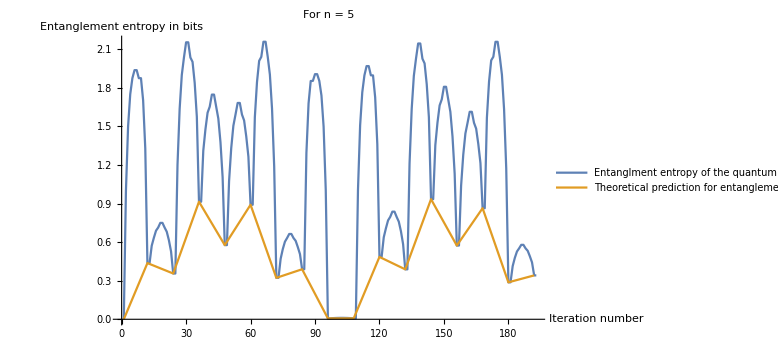

```mathematica
ListLinePlot[{lines,jumps},PlotLegends->{"Entanglment entropy of the quantum state during a simulation of Grover’s algorithm","Theoretical
prediction for entanglement entropy between iterations of Grover's algorithm "},AxesLabel->{"Iteration number","Entanglement entropy in bits"},ImageSize->Large,PlotLabel->"For n = 5"]
```

## Quantum inspired Grover’s Algorithm

Generate oracle operator as in Eq.4

```mathematica
uw=QuantumOperator["Identity",Range[n]]-2QuantumState[bitstring]["Operator"]
```

QuantumOperator[…]

The original bitstring we considered

```mathematica
bitstring
```

10101

Test that above oracle is the same as the one we get automatically from PhaseOracle

```mathematica
uw==QuantumCircuitOperator[{"PhaseOracle",BooleanFunction[2^2^^10101]}]["CircuitOperator"]
```

True

Generate diffusion operator

```mathematica
us=QuantumOperator["Identity",Range[n]]-2QuantumState[{"UniformSuperposition",n}]["Operator"]
```

QuantumOperator[…]

Test it is the same as the one we get automatically from GroverPhaseDiffusion

```mathematica
us==QuantumCircuitOperator[{"GroverPhaseDiffusion",n}]["CircuitOperator"]
```

True

Running through the steps of QiGA

```mathematica
psiw=uw[QuantumState[{"UniformSuperposition",n}]]
```

QuantumState[…]

Do the subtraction, as explained in Step-2 of page 6 in the paper:

```mathematica
wt=psiw-QuantumState[{"UniformSuperposition",n}]
```

QuantumState[…]

Show it follows the expected formula:

```mathematica
wt//TraditionalForm
```

-10101/(2 √2)

which is the same as Eq.15 of the paper (with n=5). Note S=1 in the example we considered here.

MPS stands for Matrix Product State and refers to a tensor network representation of a quantum state .  MPS provides a compact and efficient way to describe the quantum state of a system composed of multiple particles or qubits . In an MPS, the quantum state is represented as a product of tensors, where each tensor describes the state of an individual particle or qubit and its connections to neighboring particles . The key idea behind the MPS representation is that the state of each particle depends only on its local environment, allowing for an efficient and tractable description of the overall quantum state . The tensors in an MPS are typically chosen to have a low bond dimension, meaning that they have a small number of indices or parameters . This low bond dimension property enables efficient computations and manipulations of the quantum state.

Sampling from the MPS of state W

```mathematica
qsmps=QuantumStateMPS[QuantumState[wt]];
qsmps[]["Probability"]
```

<|10101→1|>

The sawtooth-shaped trend observed for the rank of the MPS of W carries significant implications. The rank of the MPS corresponds to the “amount” of entanglement present in the quantum system during the execution of Grover’s algorithm. In this paper, the observed sawtooth pattern highlights the oscillation of entanglement entropy as the algorithm progresses through its iterations. The significance of this sawtooth-shaped trend lies in its relation to the efficiency and effectiveness of Grover’s algorithm. As the algorithm advances, the entanglement between qubits increases, leading to higher values of the MPS rank.

Compute the MPS for each step

```mathematica
mpsList=QuantumStateMPS/@steps3;
```

A function to compute the rank of MPS

```mathematica
bondDimension[mps_]:=Intersection@@@({#1["OutputDimensions"],#2["InputDimensions"]}&@@@Partition[mps["Operators"],2,1])
```

Get the rank for all steps

```mathematica
rank=Flatten[DeleteDuplicates/@(bondDimension/@mpsList)];
```

Plot it together with entropies

```mathematica
ListLinePlot[{lines[[;;Length[rank]]],rank},MultiaxisArrangement->True,PlotLegends->Automatic]
```

-Graphics-

## Future Directions

This project focused on investigating the claims presented in a recent paper, starting with the simplest case of a search space consisting of 5 qubits and 1 target element. We successfully replicated the procedure outlined in the paper and observed a similar trend in the entanglement entropy during the simulation of Grover’s algorithm. Moreover, we verified that the algorithm employed by the authors is an alternative implementation of Grover’s algorithm. However, this work can be expanded upon by running the same simulations with larger number of qubits and number of target elements .Further, it is required to thoroughly examine their claims regarding the complexity of their algorithm, which is stated to be O(log N), and to compare it with Grover’s algorithm on real quantum computers. Additionally, exploring the practical implications and limitations of their algorithm in real-world scenarios would be an essential area for future investigation. One important step that we believe needs more investigation is the measurement step, which will add more complexity into calculations.

## Concluding Remarks

In conclusion, this project successfully demonstrated the procedure outlined in the paper for a single target element search problem within Grover’s algorithm. However, it is important to acknowledge that due to time constraints and limitations in computational power, expanding the scope of the project to include a larger number of qubits and an increased number of solutions was not feasible. Nonetheless, this work serves as a valuable foundation for future investigations that can build upon the findings presented here and explore the potential of Grover’s algorithm in more complex search scenarios.

## Keywords

Quantum Computing

Complexity

Grover’s Algorithm

Quantum Entanglement Entropy

## Acknowledgment

I am deeply grateful for Stephen Wolfram’s thought-provoking idea that has fueled my motivation throughout the course of this project. I express my sincere gratitude to Mads Bahrami, Nik Murzin and Shivam Sawarn for their exceptional explanations and valuable guidance. Their expertise and advice have been invaluable throughout my learning journey. Likewise, I would also like to thank Xerxes D. Arsiwalla for his continued support. I would like to extend my appreciation to all the fellow students in the physics track. Their presence and friendship have greatly contributed to making the summer school an incredibly enjoyable and enriching experience.

## References

arXiv:2303.11317v1 [quant-ph] 20 Mar 2023

https://resources.wolframcloud.com/ExampleRepository/resources/Grovers-search-algorithm/